```mathematica
(* This file looks at diffusion algorithm projection to a sphere and cylinder after 3D diffusion.  The two options are to project directly to the sphere or cylinder or to first project to a plane that is normal to the sphere or cylinder and then project from the plane to the sphere or cylinder.  I was thinking that the latter method would be better.  However this file shows clearly that the former method is better and in fact is surprisingly accurate. *)
```

```mathematica
(*************************)
(* Define some functions *)
(*************************)
```

```mathematica
(* Gaussian *)
gauss[x_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-x^2/(2*sigma^2)]
```

```mathematica
(* Produces a random gaussian deviate centered at 0 with std. dev. sigma *)
randomvect[sigma_]:=RandomVariate[MultinormalDistribution[{0,0,0},{{sigma^2,0,0},{0,sigma^2,0},{0,0,sigma^2}}]]
```

```mathematica
(* Projects vector to x-y plane which has given z value *)
project2plane[xvect_,z_]:={xvect[[1]],xvect[[2]],z}
```

```mathematica
(* Projects vector to sphere of given radius that is centered about origin. *)
project2sphere[xvect_,radius_]:=Module[{ratio},
ratio=radius/Sqrt[xvect[[1]]^2+xvect[[2]]^2+xvect[[3]]^2];
ratio*xvect]
```

```mathematica
(* Projects vector to cylinder of given radius that is along x-axis. *)
project2cylinder[xvect_,radius_]:=Module[{ratio},
ratio=radius/Sqrt[xvect[[2]]^2+xvect[[3]]^2];
Return[{xvect[[1]],xvect[[2]]*ratio,xvect[[3]]*ratio}]]
```

```mathematica
(* Compute polar angle in spherical coordinates for given vector.  This angle is angle away from z axis. *)
computetheta[xvect_]:=ArcTan[xvect[[3]],Sqrt[xvect[[1]]^2+xvect[[2]]^2]]
```

```mathematica
(* Compute cylinder angle value for given vector.  This angle is angle away from z axis for a cylinder on x axis. *)
computecylangle[xvect_]:=ArcTan[xvect[[3]],xvect[[2]]]
```

```mathematica
(* Diffuse on sphere surface starting from xvect.  Runs for total standard deviation sigma but performed in given number of steps. *)
diffusemultistep[xvect_,sigma_,radius_,steps_]:=Module[{x,s},
x=xvect;
s=sigma/Sqrt[steps];
For[i=1,i≤steps,i++,{
x=x+randomvect[s];
x=project2sphere[x,radius]; }];
Return[x]]
```

```mathematica
(* Diffuse on cylinder starting from xvect.  Runs for total standard deviation sigma but performed in given number of steps. *)
diffusecylmultistep[xvect_,sigma_,radius_,steps_]:=Module[{x,s},
x=xvect;
s=sigma/Sqrt[steps];
For[i=1,i≤steps,i++,{
x=x+randomvect[s];
x=project2cylinder[x,radius]; }];
Return[x]]
```

```mathematica
(* Takes a list of values and converts this to a histogram that can be graphed using the given bin width.  Result should integrate to 1. *)
histlist[dist_,binwidth_]:=Module[{hist},
hist=HistogramList[dist,{binwidth}];
hist[[1]]=hist[[1]]-binwidth/2;
hist[[1]]=Drop[hist[[1]],1];
hist[[2]]=hist[[2]]/Total[hist[[2]]]/binwidth;
Return[Transpose[hist]]];
```

```mathematica
(* Theory for cylinder distribution.  Assumes that sigma is less than about Pi *)
cyltheory[theta_,sigma_]:=gauss[theta,sigma]+gauss[2*Pi+theta,sigma]+gauss[-2*Pi+theta,sigma]
```

```mathematica
(* Theory for sphere distribution.  Result is eq. 7 from Ghosh_Sinha_2012. *)
spheretheory[theta_,sigma_]:=Sin[theta]/2*Sum[(2*l+1)*Exp[-l*(l+1)*sigma^2/2]*LegendreP[l,Cos[theta]],{l,0,30}]
```

```mathematica
(*****************)
(* Test fuctions *)
(*****************)
```

```mathematica
x={0,0,1}+randomvect[0.1]
```

{-0.160125,0.0912113,0.814071}

```mathematica
project2plane[x,5]
```

{-0.160125,0.0912113,5}

```mathematica
x2=project2sphere[x,1]
```

{-0.191842,0.109279,0.975323}

```mathematica
Norm[x2]
```

1.

```mathematica
computetheta[x2]
```

0.222617

```mathematica
diffusemultistep[{0,0,1},1,1,10]
```

{0.692725,0.354001,0.628343}

```mathematica
(************************************)
(* Compute distributions for sphere *)
(************************************)
```

```mathematica
(* Sphere has radius 1.  s is rms step length.  binwidth is histogram bin width in radians.  samples is number of random samples. *)
```

```mathematica
s=0.5
binwidth=0.1
samples=100000
```

0.5

0.1

100000

```mathematica
distdirect2sphere=Table[computetheta[project2sphere[{0,0,1}+randomvect[s],1]],{samples}];
```

```mathematica
disttwostep=Table[computetheta[project2sphere[project2plane[{0,0,1}+randomvect[s],1],1]],{samples}];
```

```mathematica
histdirect2sphere=histlist[distdirect2sphere,binwidth];
histtwostep=histlist[disttwostep,binwidth];
```

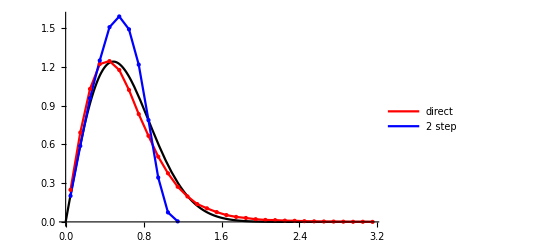

```mathematica
Show[{Plot[spheretheory[theta,s],{theta,0,Pi},PlotStyle->Black],ListLinePlot[{histdirect2sphere,histtwostep},PlotLegends->{"direct","2 step"},PlotStyle->{Red,Blue}],
ListPlot[{histdirect2sphere,histtwostep},PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]}]},PlotRange->All,AxesStyle->Directive[Bold,12]]
```

```mathematica
(* Look at statistics for different methods.  This is mean value. *)
NIntegrate[theta*spheretheory[theta,s],{theta,0,Pi}]
Mean[distdirect2sphere]
Mean[disttwostep]
```

0.613338

0.615148

0.528156

```mathematica
(* More statistics.  This is rms step length on sphere surface.  The factor of 2 is here because this is 2D diffusion where the mean squared step length is 4Dt rather than 2Dt. *)
sphstddev=Sqrt[NIntegrate[theta^2*spheretheory[theta,s]/2,{theta,0,Pi}]]
{x=Sqrt[Total[distdirect2sphere^2]/Length[distdirect2sphere]/2],x/sphstddev}
{x=Sqrt[Total[disttwostep^2]/Length[disttwostep]/2],x/sphstddev}
```

0.489275

{0.509958,1.04227}

{0.405009,0.827774}

```mathematica
(* Sphere calculations, combined to single functions. *)
stddevsphereexact[s_]:=Sqrt[NIntegrate[theta^2*spheretheory[theta,s]/2,{theta,0,Pi}]];
stddevspheredirect[s_,samples_]:=Module[{dist,stddev},
dist=Table[computetheta[project2sphere[{0,0,1}+randomvect[s],1]],{samples}];
stddev=Sqrt[Total[dist^2]/Length[dist]/2];
Return[stddev]];
stddevspheretwostep[s_,samples_]:=Module[{dist,stddev},
dist=Table[computetheta[project2sphere[project2plane[{0,0,1}+randomvect[s],1],1]],{samples}];
stddev=Sqrt[Total[dist^2]/Length[dist]/2];
Return[stddev]];
```

```mathematica
stddevsph=Transpose[Table[{{s,stddevsphereexact[s]},{s,stddevspheredirect[s,100000]},{s,stddevspheretwostep[s,100000]}},{s,0.1,1.5,0.1}]];
```

```mathematica
stddevsph={Prepend[stddevsph[[1]],{0,0}],Prepend[stddevsph[[2]],{0,0}],Prepend[stddevsph[[3]],{0,0}]};
```

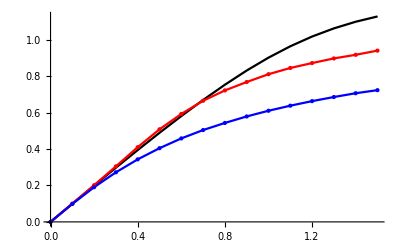

```mathematica
Show[{ListLinePlot[stddevsph,PlotStyle->{Black,Red,Blue}],
ListPlot[stddevsph,PlotStyle->{Directive[Black,PointSize[0]],Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]}]},AxesStyle->Directive[Bold,12]]
```

```mathematica
stddevsph[[1,2;;11,1]]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
(* Maximum fractional error for s between 0 and 1 for direct and 2 step *)
Max[Abs[stddevsph[[2,2;;11,2]]/stddevsph[[1,2;;11,2]]-1]]
Max[Abs[stddevsph[[3,2;;11,2]]/stddevsph[[1,2;;11,2]]-1]]
```

0.100786

0.32327

```mathematica
(*************************************)
(* Compute distributions for cylinder *)
(*************************************)
```

```mathematica
s=0.5
binwidth=0.1
samples=100000
```

0.5

0.1

100000

```mathematica
distdirect2cyl=Table[computecylangle[project2cylinder[{0,0,1}+randomvect[s],1]],{samples}];
```

```mathematica
distcyltwostep=Table[computecylangle[project2cylinder[project2plane[{0,0,1}+randomvect[s],1],1]],{samples}];
```

```mathematica
histdirect2cyl=histlist[Abs[distdirect2cyl],binwidth];
histcyltwostep=histlist[Abs[distcyltwostep],binwidth];
```

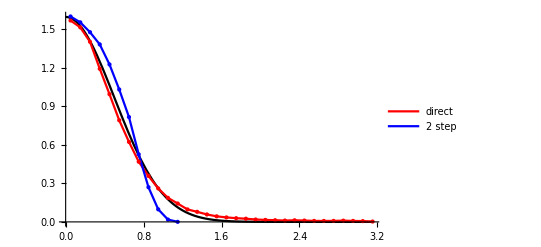

```mathematica
Show[{Plot[2*cyltheory[theta,s],{theta,0,Pi},PlotStyle->Black],ListLinePlot[{histdirect2cyl,histcyltwostep},PlotLegends->{"direct","2 step"},PlotStyle->{Red,Blue}],
ListPlot[{histdirect2cyl,histcyltwostep},PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]}]},PlotRange->All,AxesOrigin->{0,0},AxesStyle->Directive[Bold,12]]
```

```mathematica
(* Look at statistics for different methods *)
cylstddev=Sqrt[NIntegrate[theta^2*cyltheory[theta,s],{theta,-Pi,Pi}]]
{x=StandardDeviation[distdirect2cyl],x/cylstddev-1}
{x=StandardDeviation[distcyltwostep],x/cylstddev-1}
```

0.5

{0.606663,0.213326}

{0.424021,-0.151958}

```mathematica
(* Cylinder calculations, combined to single functions. *)
stddevcylexact[s_]:=Sqrt[NIntegrate[theta^2*cyltheory[theta,s],{theta,-Pi,Pi}]];
stddevcyldirect[s_,samples_]:=Module[{dist,stddev},
dist=Table[computecylangle[project2cylinder[{0,0,1}+randomvect[s],1]],{samples}];
stddev=StandardDeviation[dist];
Return[stddev]];
stddevcyltwostep[s_,samples_]:=Module[{dist,stddev},
dist=Table[computecylangle[project2cylinder[project2plane[{0,0,1}+randomvect[s],1],1]],{samples}];
stddev=StandardDeviation[dist];
Return[stddev]];
```

```mathematica
stddevcyl=Transpose[Table[{{s,stddevcylexact[s]},{s,stddevcyldirect[s,100000]},{s,stddevcyltwostep[s,100000]}},{s,0.1,1.5,0.1}]];
```

```mathematica
stddevcyl={Prepend[stddevcyl[[1]],{0,0}],Prepend[stddevcyl[[2]],{0,0}],Prepend[stddevcyl[[3]],{0,0}]};
```

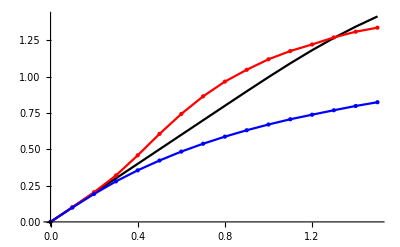

```mathematica
Show[{ListLinePlot[stddevcyl,PlotStyle->{Black,Red,Blue}],
ListPlot[stddevcyl,PlotStyle->{Directive[Black,PointSize[0]],Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]}]},AxesStyle->Directive[Bold,12]]
```

```mathematica
(* Maximum fractional error for s between 0 and 1 *)
Max[Abs[stddevcyl[[2,2;;11,2]]/stddevcyl[[1,2;;11,2]]-1]]
Max[Abs[stddevcyl[[3,2;;11,2]]/stddevcyl[[1,2;;11,2]]-1]]
```

0.239383

0.327296